Fitting MagneticTB bands to VASP

To fit a tight-binding model to VASP bands, first read EIGENVAL and construct the Hamiltonian from symmetry. Here we fit three bands with a three-orbital model, compare nearest-neighbor and second-neighbor results, and then fit a selected energy or k-point range. Plot the fitted and VASP bands together to see both the agreement and any remaining differences.

```mathematica
Needs["MagneticTB`"]
```

Read and inspect the three VASP bands

Use vaspEig to read bands 21-23 and subtract the Fermi energy. First plot all three bands to see the reference band structure:

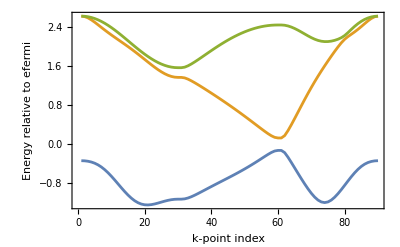

```mathematica
eigenvalFile = FileNameJoin[{
  NotebookDirectory[],
  "..", "ReferencePages", "Symbols", "EIGENVAL"
}];
vaspBands = vaspEig[eigenvalFile, -0.0072, 1, 21, 23];
ListLinePlot[
  Transpose[vaspBands[[All, 2]]],
  Frame -> True,
  FrameLabel -> {"k-point index", "Energy relative to efermi"},
  PlotRange -> All
]
```

Build the symmetry-generated model

For this three-orbital model, take the first six operations from msgop[gray[156]], which form its complete unitary subgroup. The onsite and nearest-neighbor terms contain e1, e2, and t1-t9. These are the parameters to be fitted:

```mathematica
init[
  lattice -> {
    {a, 0, 0},
    {-a/2, Sqrt[3] a/2, 0},
    {0, 0, c}
  },
  lattpar -> {a -> 1, c -> 10},
  wyckoffposition -> {{{2/3, 1/3, 0}, {0, 0, 0}}},
  symminformation -> Take[msgop[gray[156]], 6],
  basisFunctions -> {{"dz2", "dxy", "dx2-y2"}},
  InitialBondShells -> 3
];
fittingHamiltonian = symham[1] + symham[2];
fittingPath = {
  {{{0, 0, 0}, {1/2, 0, 0}}, {"Γ", "M"}},
  {{{1/2, 0, 0}, {1/3, 1/3, 0}}, {"M", "K"}},
  {{{1/3, 1/3, 0}, {0, 0, 0}}, {"K", "Γ"}}
};
initialRules = {
  e1 -> 0.915, e2 -> 0.685,
  t1 -> 0.1, t2 -> 0.09, t3 -> 0.1,
  t4 -> -0.38, t5 -> 0.34, t6 -> 0.245,
  t7 -> 0.565, t8 -> 0.305, t9 -> 0.365
};
```

Fit the onsite and nearest-neighbor model

Fit the three bands at all 90 k points. Then draw them together with the VASP bands:

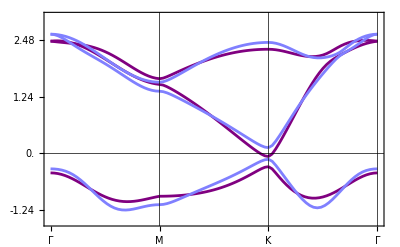
-Graphics-Purple: TB, Blue: VASP

```mathematica
nearestFit = fittingTB[
  fittingHamiltonian, vaspBands,
  Range[Length[vaspBands]], initialRules
];
compareBand[
  fittingPath, 30, fittingHamiltonian,
  nearestFit["FittedParams"], vaspBands,
  plotRange -> {-1.5, 3}
]
```

Add second-neighbor hopping

To include second-neighbor hopping, keep the fitted nearest-neighbor parameters as the initial values and set the new parameters r1-r10 to zero. Fit again and compare the two band plots to see where the extra hoppings improve the agreement.

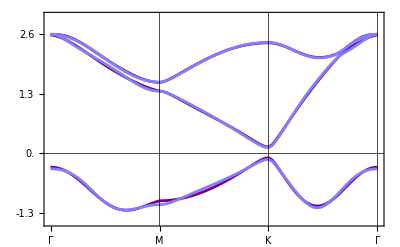
-Graphics-Purple: TB, Blue: VASP

```mathematica
secondNeighborHamiltonian = fittingHamiltonian + symham[3];
secondNeighborInitialRules = Join[
  nearestFit["FittedParams"],
  Thread[{r1, r2, r3, r4, r5, r6, r7, r8, r9, r10} -> 0.]
];
secondNeighborFit = fittingTB[
  secondNeighborHamiltonian, vaspBands,
  Range[Length[vaspBands]], secondNeighborInitialRules
];
compareBand[
  fittingPath, 30, secondNeighborHamiltonian,
  secondNeighborFit["FittedParams"], vaspBands,
  plotRange -> {-1.5, 3}
]
```

Fit the energy range of interest

If only bands near the Fermi energy are of interest, set EnergyWindow to the desired energy interval. Only reference energies in this interval enter the fit. The plot still shows the full bands, so changes outside the interval can also be seen.

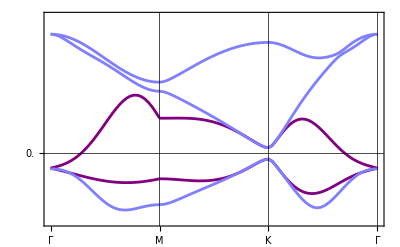
-Graphics-Purple: TB, Blue: VASP

```mathematica
fermiFit = fittingTB[
  fittingHamiltonian, vaspBands,
  Range[Length[vaspBands]], initialRules,
  "EnergyWindow" -> {-0.5, 0.5}
];
compareBand[
  fittingPath, 30, fittingHamiltonian,
  fermiFit["FittedParams"], vaspBands,
  plotRange -> {-1.5, 3}
]
```

Fit near the K point

To fit near K, set KPointNeighborhood to K and radius 0.15 in reciprocal fractional coordinates. Distances include periodic equivalents of k points. ComparisonPlot displays only this neighborhood: blue points are VASP, gray dashed curves are the initial model, and red curves are the fitted model.

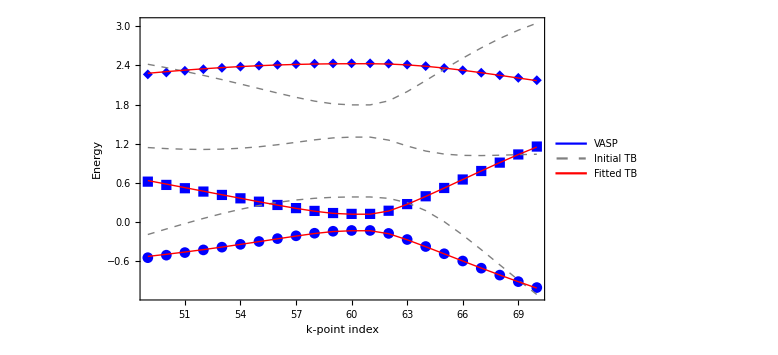

```mathematica
kFit = fittingTB[
  fittingHamiltonian, vaspBands,
  Range[Length[vaspBands]], initialRules,
  "KPointNeighborhood" -> <|
    "Center" -> {1/3, 1/3, 0},
    "Radius" -> 0.15,
    "Periodic" -> True
  |>
];
kFit["ComparisonPlot"]
```

Judge the plotted bands, not only the loss

fittingTB compares sorted model eigenvalues with the corresponding reference energies. It does not impose a gap or track orbital character and band connectivity. A small energy error alone is therefore not enough: also compare gaps and crossings in the plot. Use physically reasonable initial parameters, and retain the fitted values when adding more neighbor hoppings.

Related functions

vaspEig   bandManipulateEig   fittingTB   compareBand

MagneticTB help home

MagneticTB

History